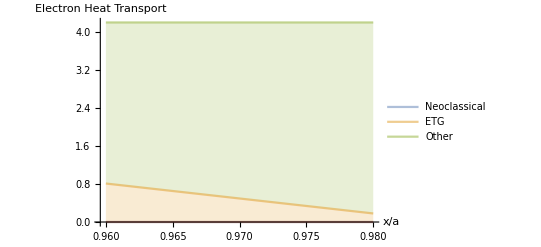

```mathematica
Plottot=Range[4];
{Plottot[[1]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\conference\\Plots\\Transport\\NEO.xlsx"];
{Plottot[[2]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\conference\\Plots\\Transport\\ETG.xlsx"];
{Plottot[[3]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\conference\\Plots\\Transport\\TOT.xlsx"];
{Plottot[[4]]}=Import["C:\\Users\\maxcu\\Google Drive\\0Research\\conference\\Plots\\Transport\\TOT.xlsx"];

For[i=1,i<Length[Plottot[[1]]]+1,i++,
Plottot[[2]][[i]][[2]]=Plottot[[2]][[i]][[2]]+Plottot[[1]][[i]][[2]];
Plottot[[4]][[i]][[1]]=Plottot[[1]][[i]][[1]];
Plottot[[4]][[i]][[2]]=0
]

ListPlot(*ListPlot*)[
Plottot,
Joined->True,

AxesLabel->{Style["x/a"
,Bold,15],
Style["Electron Heat Transport"
,Bold,15]},
Filling->{{1->{4}},{2->{1}},{3->{2}}},
(*PlotRange->{{0,10},{0,0.08}},*)
PlotStyle->Directive[Opacity[0.5],Automatic],
(*PlotMarkers->{Automatic,Small},*)
AxesStyle->Directive[Black,15],
PlotLegends->{ToExpression["Neoclassical",TeXForm
]
,
ToExpression["ETG",TeXForm
]
,
ToExpression["Other",TeXForm
]
}

]
```